# ANOMS ANZ@SFO Data Analysis

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/ANOMS/SFO ANOMS"]
sfoanomsdays=FileNames[];
Length[sfoanomsdays]
sfoanomsdays[[1]]//FullForm  (* a sample *)
```

/Users/brucesawhill/Desktop/ANOMS/SFO ANOMS

261

"20060201.lt6"

```mathematica
FileNames[]
```

{20060201.lt6,20090615.lt6,20090616.lt6,20090617.lt6,20090618.lt6,20090619.lt6,20090620.lt6,20090621.lt6,20090622.lt6,20090623.lt6,20090624.lt6,20090625.lt6,20090626.lt6,20090627.lt6,20090628.lt6,20090629.lt6,20090630.lt6,20090701.lt6,20090702.lt6,20090703.lt6,20090704.lt6,20090705.lt6,20090706.lt6,20090707.lt6,20090708.lt6,20090709.lt6,20090710.lt6,20090711.lt6,20090712.lt6,20090713.lt6,20090714.lt6,20090715.lt6,20090716.lt6,20090717.lt6,20090718.lt6,20090719.lt6,20090720.lt6,20090721.lt6,20090722.lt6,20090723.lt6,20090724.lt6,20090725.lt6,20090726.lt6,20090727.lt6,20090728.lt6,20090729.lt6,20090730.lt6,20090731.lt6,20090801.lt6,20090802.lt6,20090803.lt6,20090804.lt6,20090805.lt6,20090806.lt6,20090807.lt6,20090808.lt6,20090809.lt6,20090810.lt6,20090811.lt6,20090812.lt6,20090813.lt6,20090814.lt6,20090815.lt6,20090816.lt6,20090817.lt6,20090818.lt6,20090819.lt6,20090820.lt6,20090821.lt6,20090822.lt6,20090823.lt6,20090824.lt6,20090825.lt6,20090826.lt6,20090827.lt6,20090828.lt6,20090829.lt6,20090830.lt6,20090831.lt6,20090901.lt6,20090902.lt6,20090903.lt6,20090904.lt6,20090905.lt6,20090906.lt6,20090907.lt6,20090908.lt6,20090909.lt6,20090910.lt6,20090911.lt6,20090912.lt6,20100829.lt6,20101007.lt6,20101123.lt6,20101124.lt6,20101126.lt6,20101128.lt6,20101129.lt6,20101130.lt6,20101201.lt6,20101202.lt6,20101203.lt6,20101204.lt6,20101205.lt6,20101206.lt6,20101207.lt6,20101208.lt6,20101209.lt6,20101210.lt6,20101211.lt6,20101212.lt6,20101213.lt6,20101214.lt6,20101215.lt6,20101216.lt6,20101217.lt6,20101218.lt6,20101219.lt6,20101220.lt6,20101221.lt6,20101222.lt6,20101223.lt6,20101224.lt6,20101225.lt6,20101226.lt6,20101227.lt6,20101228.lt6,20101229.lt6,20101230.lt6,20101231.lt6,20110101.lt6,20110102.lt6,20110103.lt6,20110104.lt6,20110105.lt6,20110106.lt6,20110107.lt6,20110108.lt6,20110109.lt6,20110110.lt6,20110111.lt6,20110112.lt6,20110113.lt6,20110114.lt6,20110115.lt6,20110116.lt6,20110117.lt6,20110118.lt6,20110119.lt6,20110120.lt6,20110121.lt6,20110122.lt6,20110123.lt6,20110124.lt6,20110125.lt6,20110126.lt6,20110127.lt6,20110128.lt6,20110129.lt6,20110130.lt6,20110131.lt6,20110201.lt6,20110202.lt6,20110203.lt6,20110204.lt6,20110205.lt6,20110206.lt6,20110207.lt6,20110208.lt6,20110209.lt6,20110210.lt6,20110211.lt6,20110212.lt6,20110213.lt6,20110214.lt6,20110215.lt6,20110216.lt6,20110217.lt6,20110218.lt6,20110219.lt6,20110220.lt6,20110221.lt6,20110222.lt6,20110223.lt6,20110224.lt6,20110225.lt6,20110226.lt6,20110227.lt6,20110228.lt6,20110301.lt6,20110302.lt6,20110303.lt6,20110304.lt6,20110305.lt6,20110306.lt6,20110307.lt6,20110308.lt6,20110309.lt6,20110310.lt6,20110311.lt6,20110312.lt6,20110313.lt6,20110314.lt6,20110315.lt6,20110316.lt6,20110317.lt6,20110318.lt6,20110319.lt6,20110320.lt6,20110321.lt6,20110322.lt6,20110323.lt6,20110324.lt6,20110325.lt6,20110326.lt6,20110327.lt6,20110328.lt6,20110329.lt6,20110330.lt6,20110331.lt6,20110401.lt6,20110402.lt6,20110403.lt6,20110404.lt6,20110405.lt6,20110406.lt6,20110407.lt6,20110408.lt6,20110409.lt6,20110410.lt6,20110411.lt6,20110412.lt6,20110413.lt6,20110414.lt6,20110415.lt6,20110416.lt6,20110417.lt6,20110418.lt6,20110419.lt6,20110420.lt6,20110421.lt6,20110422.lt6,20110423.lt6,20110424.lt6,20110425.lt6,20110426.lt6,20110427.lt6,20110428.lt6,20110429.lt6,20110430.lt6,20110501.lt6,20110502.lt6,20110503.lt6,20110504.lt6,20110504.txt,2013_08_29_sample,.DS_Store,filterednzflights,nzflights,SFO_ANOMS_2006-2011.zip,sfo.avi}

Accessory Functions

```mathematica
interpolated[data_]:=
{
offsettime = AbsoluteTime[StringJoin[data[[3,1]],"/",data[[4,1]]]];
ld = Length[data];
totaltime = data[[ld,5]];
newdatatable =Table[{},{totaltime+1}]; (* Make a one-second resolution dataset*)
newdatatable[[1]] = data[[21]];
p = 2;(* Set interpolating index *)

Do[
diff = data[[i+1,5]]-data[[i,5]];
Do[
{
newdatatable[[p]]=(diff-j)/diff data[[i]]+j/diff data[[i+1]]; (* Interpolate *)
p++
}
,{j, 1, diff}
]
,{ i, 21,ld-1}
]
Do[newdatatable[[k,5]]=newdatatable[[k,5]]+offsettime, {k, totaltime+1}];
newdatatable
}
```

This plots the location of the aircraft when making a video

```mathematica
acpointplot[proxdata_,pingindex_] := 
 Show[DeleteCases[Table[If[Length[proxdata[[i,pingindex]]]==2, ListPlot[{proxdata[[i,pingindex]]}, 
   PlotRange -> {{-100000, 100000}, {-100000, 100000}}, 
   PlotStyle -> {PointSize[1/20], Opacity[0.2], If[i==1,Red,Blue]}]],{i,Length[proxdata]}],Null]]
```

This plots the contrail leading up to the aircraft when making a video

```mathematica
contrailplot[proxdata_,pingindex_]:=
{
contrails =Table[{},{Length[proxdata]}];
 
Do[contrails[[i]] = 
Table[
If[
Length[proxdata[[i,j]]]≠2, Null,proxdata[[i,j]]
],{j,1,pingindex}
],{i,Length[proxdata]}
];

For[i = 1,i <= Length[contrails], i++, 
{
If[contrails[[i,-1]]==Null , contrails[[i]]=={{}}];
DeleteCases[contrails[[i]],Null]
}
];

DeleteCases[contrails, {{}}];

Show[
Table[
ListPlot[
contrails[[i]],PlotRange->{{-100000,100000},{-100000,100000}},Joined->True
], {i, Length[contrails]}
]
]
}[[1]]
```

This finds a candidate track for interference with a given flight

```mathematica
trackcandidate[flightrecord_]:=
If[flightrecord[[12,1]] =="A",
If[flightrecord[[13,1]]=="SFO",
If[flightrecord[[15,1]]=="28R",
True
]
]
]
```

This finds the start of each flight record by searching for the string "TRACK"

```mathematica
recordstartindices[data_]:=
{
rsi={};
ctr=0;

Do[
{
If[
StringQ[data[[i,1]]]==True,
{ (*  First the data element has to be a string *)
If[
StringLength[data[[i,1]]]≥5,(* Of sufficient length *)
 {
If[
StringTake[data[[i,1]],5]=="TRACK", (* Above two If[]'s avoid error messages here *)
{
ctr++,
rsi=Append[rsi,i];
}
]
}
]
}
]
}, {i, Length[data]}
];
rsi
}[[1]]
```

Once tracks have been parsed out, look for tracks that represent ANZ flights.

```mathematica
stringselect[data_, string_, recordstartindices_]:=
{
selections = {};
For[
i=1, i≤ctr,i++,
{
flight = data[[recordstartindices[[i]]+6,1]], (*  Check for airline code of each track *)

If[
StringQ[flight] == True, (*  Sometimes this record is an empty set *)
If[
StringLength[flight]≥3, (*  Or this record is too short *)
If[
StringTake[flight,3]==string, selections = Append[selections,i]  (* Load track numbers of ANZ flights *)
]
]
]
}
];
selections
}[[1]]
```

```mathematica
ss=stringselect[data,"ANZ",rs]
```

{}

{1100,3106}

```mathematica
pickdata[data_,recordstartindices_,flightrecordnumbers_]:=
{output = {};
If[
Length[flightrecordnumbers]≥1, (* If selections are not the empty set *)
Do[
{
newaddition = Take[data, {recordstartindices[[flightrecordnumbers[[i]]]], recordstartindices[[flightrecordnumbers[[i]]+1]]-1}],
Print[newaddition],
AppendTo[output,newaddition]   (* Pick out and add record from data *)
},{i, Length[flightrecordnumbers]}
]
];
output
}
```

Main

The grand loop to go through all of the data file and pick out all of the ANZ (or any other) flights

```mathematica
nzflights = {};
Do[
ss = 0;
rs = 0;
{
data=Import[sfoanomsdays[[j]], "CSV"];
Print[sfoanomsdays[[j]]],
Print["datalength = ", Length[data]],
rs = recordstartindices[data];
ss = stringselect[data, "ANZ",rs];

If[
Length[ss]≥1, (* If selections are not the empty set *)

Do[
{
newaddition = Take[data, {rs[[ss[[i]]]], rs[[ss[[i]]+1]]-1}],
Print["Length[ss] = ",Length[ss]],
AppendTo[nzflights,newaddition]   (* Pick out and add record from data *)
},{i, Length[ss]}
]

];
Print[j],
(*Clear[data]*)
}, {j,4,4}
]//Timing
```

20090617.lt6

datalength = 700855

Length[ss] = 2

Length[ss] = 2

4

{14.1464,Null}

Parse out flights up to 450 seconds before ANZ flight.

```mathematica
nzlandtime = AbsoluteTime[StringJoin[Take[data, {rs[[ss[[1]]]]+2}][[1,1]],"/",Take[data, {rs[[ss[[1]]]]+4}][[1,1]]]]; (* Benchmark time *)
beforeindices = {};
numflightsbefore = 1;
deltat = 0;
While[deltat ≤450, (*Go back in time to find close flights*)
{fr = Take[data,{rs[[ss[[1]]-numflightsbefore]],
rs[[ss[[1]]-numflightsbefore+1]]-1}];
If[
trackcandidate[fr]==True,
{
time = AbsoluteTime[StringJoin[fr[[3,1]],"/",fr[[5,1]]]],
deltat=nzlandtime-time,
AppendTo[beforeindices,ss[[1]]-numflightsbefore],
Print[time]
}
]
};
 numflightsbefore++
]
```

3454231984

3454231892

3454231744

Parse flights up to 450 seconds after ANZ flight

```mathematica
nzlandtime = AbsoluteTime[StringJoin[Take[data, {rs[[ss[[1]]]]+2}][[1,1]],"/",Take[data, {rs[[ss[[1]]]]+4}][[1,1]]]]; (* Benchmark time *)
afterindices = {};
numflightsafter = 1;
deltat = 0;
While[deltat ≤450,(*Look forward in time to find close flights*)
{fr = Take[data,{rs[[ss[[1]]+numflightsafter]],
rs[[ss[[1]]+numflightsafter+1]]-1}];
If[
trackcandidate[fr]==True,
{
time = AbsoluteTime[StringJoin[fr[[3,1]],"/",fr[[5,1]]]],
deltat=time-nzlandtime,
AppendTo[afterindices,ss[[1]]+numflightsafter]
}
]
};
 numflightsafter++
]
```

```mathematica
afterindices
```

{1310,1312,1324,1332}

```mathematica
rs[[1]]
```

1

```mathematica
indexlist = Join[{ss[[1]]},beforeindices,afterindices]
```

{1295,1269,1262,1252,1310,1312,1324,1332}

```mathematica
locals=Table[interpolated[Take[data,{rs[[indexlist[[i]]]],rs[[indexlist[[i]]+1]]-1}]],{i,8}];
```

```mathematica
refstarttime = locals[[1,1,1,5]]
refendtime = locals[[1,1,-1,5]]
earliesttime = Min[Table[locals[[i,1,1,5]],{i,Length[locals]}]]
latesttime =  Max[Table[locals[[i,1,-1,5]],{i,Length[locals]}]]
timespread = latesttime-earliesttime
timematrix = Table[0, {j, Length[locals]},{i,timespread+1}];
Dimensions[timematrix]
refstarttime - earliesttime
refendtime-earliesttime
```

3454230533

3454232289

3454229370

3454232792

3422

{8,3423}

1163

2919

```mathematica
Do[
{offset= locals[[i,1,1,5]]-earliesttime,
Do[
timematrix[[i,j + offset]]=Take[locals[[i,1,j]],2],
{j, Length[locals[[i,1]]]}
]
},{i,8}]
```

```mathematica
trimmedtimematrix = Table[timematrix[[i,j]],{i,8},
{j,refstarttime-earliesttime+1,refendtime-earliesttime+1}];
```

```mathematica
trimmedtimematrix[[1,538]]
```

{-46353,-233892/5}

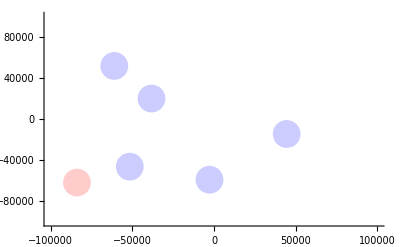

```mathematica
va=acpointplot[trimmedtimematrix,47]
```

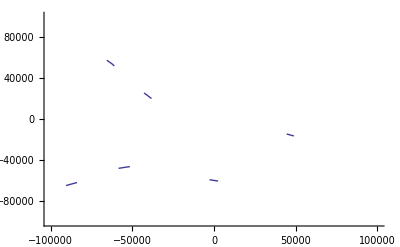

```mathematica
vb=contrailplot[trimmedtimematrix,47]
```

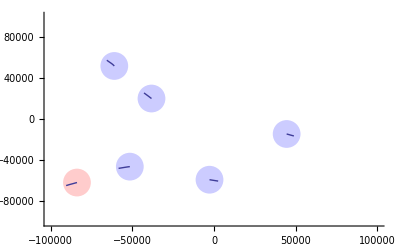

```mathematica
Show[va,vb]
```

```mathematica
runway = Point[{-12994,-9545}]
```

Point[{-12994,-9545}]

```mathematica
showrunway = Graphics[{PointSize[.03],Red,runway}];
```

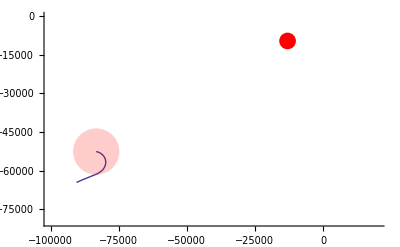

```mathematica
Show[contrailplot[trimmedtimematrix,1,138],acpointplot[trimmedtimematrix,1,138],showrunway]
```

```mathematica
frames = Table[acpointplot[trimmedtimematrix,i],{i,1,1747,5}];
```

```mathematica
Export["sfo.avi", frames];
```

```mathematica
ListAnimate[
Table[
Show[
acpointplot[trimmedtimematrix,i],contrailplot[trimmedtimematrix,i]
],{i,1,1747,5}
]
]
```

```mathematica
filterednzflights=DeleteCases[Table[If[StringMatchQ[nzflights[[i,12]][[1]],"A"]==True && (StringMatchQ[nzflights[[i,15]],"28R"][[1]]==True || 
StringMatchQ[nzflights[[i,15]],"28L"][[1]]==True), nzflights[[i]],0],{i,3, Length[nzflights]}],0];
```

```mathematica
Length[filterednzflights]
```

188

```mathematica
filterednzflights>>filterednzflights;
```

```mathematica
tableofplots=Table[ListPlot[Table[{filterednzflights[[i,j,1]],filterednzflights[[i,j,2]]},{j,21, Length[filterednzflights[[i]]]}]],{i,188}];
```

```mathematica
Show[tableofplots, PlotLabel->"30 ANZ SFO Approaches"]
```

```mathematica
nzflights = Take[nzflights, {1, 254}];
```

```mathematica
nzflights>>nzflights;
```

Fills out a dataset to one second intervals

```mathematica
AbsoluteTime[StringJoin[fr[[3,1]],"/",fr[[4,1]]]]
```

3454230533

Previous Analysis

I see it is possible to index a long list of file names because the list is an expression that can be manipulated in a standard way.

Parse the data into individual flights, separate out the trackpoints from the metadata.

```mathematica
trackmatrix=Table[{},{3088}];
startpositioncounter=1;
Do[
{
trackpoints=data[[startpositioncounter+19]][[1]];
trackmatrix[[trackindex]]=Take[data, {startpositioncounter, startpositioncounter+19+trackpoints}];
startpositioncounter=startpositioncounter+20+trackpoints
},{trackindex,  3088}
]
```

A breakout of all of the different kinds of aircraft arriving or departing SFO.

```mathematica
Sort[Tally[DeleteCases[Table[If[trackmatrix[[i,6,1]]=="SFO",trackmatrix[[i,10]],0],{i,3088}],0]], #1[[2]]>#2[[2]]&]
```

{{{J},721},{{R},162},{{T},146},{{B},66},{{H},15},{{P},6},{{U},6},{{M},1}}

Total number of aircraft using SFO

```mathematica
Plus@@Table[If[trackmatrix[[i,6,1]]=="SFO", 1],{i,3088}]
```

1123+1965 Null

Create datamatrix of track data without metadata, normalize time in seconds from 000 hrs Zulu.

```mathematica
datamatrix=Table[Take[trackmatrix[[i]],{21, Length[trackmatrix[[i]]]}], {i,1,3088}];
```

```mathematica
starttimesvector=Table[AbsoluteTime[StringJoin["01 Jan 1900"," ", trackmatrix[[i,4,1]]]],{i,3088}];
Do[
Do[
datamatrix[[i,j,5]]=datamatrix[[i,j,5]]+starttimesvector[[i]],{j,1,Length[datamatrix[[i]]]}
],{i,3088}
];
```

See how many unique seconds are represented.  If everybody is pinged at once, there should be about 1/4 or 1/5 of the seconds in a day.  If aircraft are pinged in sequence, there could be up to the number of seconds in a day, depending on where a particular aircraft is when the radar sweeps by.  The latter hypothesis seems to be true.  Aircraft are pinged by a rotating sweep that is phase distributed.

```mathematica
uniquetimes=Union[Flatten[Table[datamatrix[[i,j,5]],{i,3088},{j,Length[datamatrix[[i]]]}]]];
```

```mathematica
Length[uniquetimes]
```

73983

A filter for finding arrivals at SFO--They start at greater than 3000 meters, traveling faster than 50 m/s, end altitude less than 1000m (not actual runway elevation to allow for data dropouts), and are identified with SFO.

```mathematica
c=0;
indexlist={};
Do[
If[
(
datamatrix[[i,1,3]]≥3000
&&Mean[Table[datamatrix[[i,j,4]], {j,1,10}]]≥50
&&trackmatrix[[i,6,1]]=="SFO"
&&  Take[datamatrix[[i]],-1][[1,3]]<1000
), 
{
c++,
indexlist=Append[indexlist,i]
}], 
{i,3088}
]
Print[c]
```

529

```mathematica
indexlist
```

This adds the segments to each string of level flying that make up the missed width of the flatdetector[] detection window used to detect the level flying, as the flat elements are only detected after a certain number (6 in the function above, or 25.2 sec) of radar pings.

```mathematica
flatfix[index_,windowsize_]:={
edges={};
workvector=flats[[index]];

Do[
If[
workvector[[i]]≠0 && workvector[[i+1]]==0, 
edges=Append[edges,i]
],{i,1,Length[workvector]-1}
];

Do[
workvector[[edges[[k]]+m]]=datamatrix[[indexlist[[index]],edges[[k]]+m,3]],{k,Length[edges]},{m,windowsize}
];
};
```

```mathematica
flats=Table[flatdetector[datamatrix[[indexlist[[i]]]],6],{i,Length[indexlist]}];
```

```mathematica
levelsegs=flats;
Do[
{
flatfix[i,6],
levelsegs[[i]]=workvector
},{i,529}
]
```

```mathematica
purelevel3=Flatten[Table[DeleteCases[levelsegs[[i]],0], {i, 529}]];
```

```mathematica
Length[purelevel3]
```

15034

Level Flight Fuel Burn Analysis

```mathematica
swa=DeleteCases[Table[If[trackmatrix[[indexlist[[flatties[[i]]]],8,1]]=="SOUTHWEST AIRLINES CO",i,0],{i,74}],0]
```

{15,31,41,47,67}

```mathematica
united=DeleteCases[Table[If[trackmatrix[[indexlist[[flatties[[i]]]],8,1]]=="UNITED AIR LINES INC",i,0],{i,74}],0]
```

{8,10,19,34,35,36,43,55,56}

```mathematica
skywest=DeleteCases[Table[If[trackmatrix[[indexlist[[flatties[[i]]]],8,1]]=="SKY WEST AVIATION INC TRUSTEE",i,0],{i,74}],0]
```

{1,2,3,4,5,6,9,11,13,14,16,18,20,22,26,29,32,33,39,40,42,44,45,46,48,50,58,60,61,62,64,65,68,70,72}

```mathematica
delta=DeleteCases[Table[If[trackmatrix[[indexlist[[flatties[[i]]]],8,1]]=="DELTA AIR LINES INC",i,0],{i,74}],0]
```

{17,37,66,73}

```mathematica
sumsky=0;
Do[
{
trackflats=levelsegs[[flatties[[skywest[[i]]]]]];
sumsky+=Sum[If[trackflats[[j]]>3500, 4.2 crj200fburn[trackflats[[j]]],0],{j,Length[trackflats]}]
},
{i,Length[skywest]}
]
```